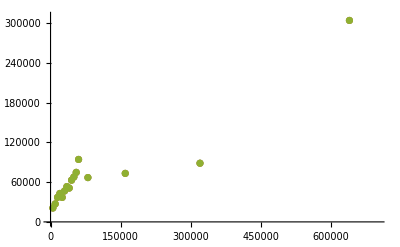

```mathematica
x = {5000, 10000,15000, 20000, 25000, 30000, 35000, 40000,45000, 50000, 55000,60000, 80000, 160000, 320000, 640000};
y = {20950, 27130, 37030, 42910, 36960, 46650, 53280, 51060, 62960, 67790, 74720, 94240, 66880, 73190, 88540, 303980};
std = {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}/Sqrt[10];
ListPlot[  {Transpose[{x,y}], Transpose[{x, y+0}],Transpose[{x, y-0}]  }, PlotRange-> {{0, 700000},{0, 310000}}]
```

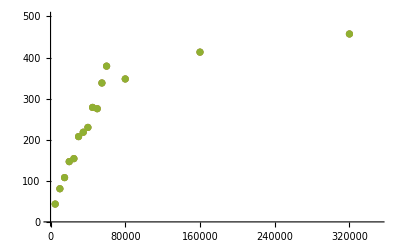

```mathematica
x  ={5000, 10000,15000, 20000, 25000, 30000, 35000, 40000,45000, 50000, 55000,60000, 80000, 160000, 320000};
roundcounts={43.4, 80.7, 107.8, 146.7, 154, 207.6, 218.2, 229.9, 278.6, 275.5,338.1, 379.1, 347.9, 413.2, 457.4};
ListPlot[{Transpose[{x,roundcounts}], Transpose[{x,roundcounts+0}],Transpose[{x, roundcounts-0}]  }, PlotRange-> {{0, 350000},{0, 500}}]
```

```mathematica
Length[x]
```

23

```mathematica
Length[roundcounts]
```

24

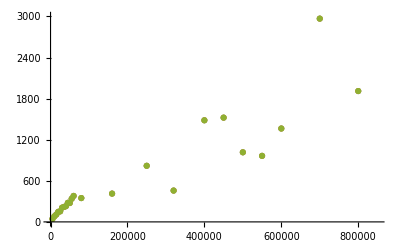

```mathematica
x  ={5000, 10000,15000, 20000, 25000, 30000, 35000, 40000,45000, 50000, 55000,60000, 80000, 160000, 250000, 320000, 400000, 450000, 500000, 550000, 600000, 700000, 800000};
roundcounts={43.4, 80.7, 107.8, 146.7, 154, 207.6, 218.2, 229.9, 278.6, 275.5,338.1, 379.1, 347.9, 413.2, 819.2, 457.4, 1483.9, 1522.5, 1016.4, 964.3, 1363.6, 2968.3, 1910.7};
ListPlot[{Transpose[{x,roundcounts}], Transpose[{x,roundcounts+0}],Transpose[{x, roundcounts-0}]  }, PlotRange-> {{0, 850000},{0, 3000}}]
```